```mathematica
Plot3D[eqblob[x,y],{x,1,10},{y,1,10}]
```

-Graphics3D-

```mathematica
solepmax=NMinimize[{eqblob[x,y],x>0,y>0},{x,y},MaxIterations->1000]
```

NMinimize::nnum: The function value 1.78346 is not a number at {x, y} = {6.69078063530148`*^-6, 0.`}.

{1.00852,{x→2.09499×10^-6,y→0.860433}}

```mathematica
eqblob[6.69*10^(-6),0.01]
```

1.74907

```mathematica
(Qradnum*Ttransit)
```

15024.3

```mathematica
npairsrad
```

1.03594×10^9

```mathematica
nrad[rhobrad,Trad,bgaussrad,npairsrad]
```

9.8965×10^12

```mathematica
FullSimplify[totaleptemp2[epmin,epmax,alphasp]]
```

(-epmax^(2-alphasp)+epmin^(2-alphasp))/(-2+alphasp)

```mathematica
it=FullSimplify[totaleptemp[epmin,epmax,alphasp]/totaleptemp2[epmin,epmax,alphasp]]
```

((-2+alphasp) (epmax epmin)^-alphasp (epmax^alphasp epmin-epmax epmin^alphasp))/((-1+alphasp) (-epmax^(2-alphasp)+epmin^(2-alphasp)))

```mathematica
god=it//.{alphasp->2.001,epmin->0.001,epmax->2}
```

131.867

```mathematica
god2=(epmax-epmin)/(epmax epmin Log[epmax]-epmax epmin Log[epmin])
```

(epmax-epmin)/(epmax epmin Log[epmax]-epmax epmin Log[epmin])

```mathematica
god/god2//.{epmax->10,epmin->0.1}
```

1.00135

```mathematica
tauhighe
```

NMinimize::nnum: The function value 0.7745497035909612`  + (-1 + 0.05244679184572666` totalxint[Min[0.00024176062668827938`, Max[0.00024139661678753343`, « 15 »]], « 2 », 2.00001`])^2 is not a number at {x, y} = {0.00024176062668827938`, 0.`}.

{1.77455,0.000241452,2.4515,0.19574}

```mathematica
( Qradnum*Habsnum)*(Pi*Rjet*Lpnum)*Ttransit
```

3.17543×10^48

```mathematica
(totaleptemp2[epmin,epmax,alphasp]/totaleptemp[epmin,epmax,alphasp])//.{epmin->0.001,epmax->10,alphasp->2.0001}
```

0.00920794

```mathematica
kb*Trad
```

5.46331×10^-8

```mathematica
npairsrad
```

1.03594×10^9

```mathematica
{epmaxerror,epmaxnum,epthicknum,epmaxobs}
```

{1.,0.0415924,6.0576×10^-8,29.4306}

```mathematica
tauradscanum
```

0.940215

```mathematica
tauradabsnum
```

3.07688×10^-11

```mathematica
(* 13 *)
```

```mathematica
eminobsMeV=0.1;
(*eminobsMeV=1.0; *)
eminobs=eminobsMeV*ergPmev/(me*c^2); (* most strict lower-limit for highest-energy photon *)
epmin=eminobs/gammavalue;
Plot3D[taugtot[epmax,epmin,epmax,epthick],{epmax,1,2000},{epthick,1,10}]
```

-Graphics3D-

```mathematica
epmaxerror
```

0.854401

```mathematica
FindRoot[funD[epmax]==0,{epmax,2}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{epmax→505.86}

```mathematica
funD[505.86]
```

2.52181×10^-11

```mathematica
myepmax=48.9486
taugtot[myepmax,epmin,myepmax,1]
```

48.9486

0.0673462

```mathematica
FindRoot[0==1-taugtot[x,epmin,x,2],{x,2*505}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→1047.12}

```mathematica
FindRoot[0==1-taugtot[x,epmin,x,2],{x,505/2}]
```

{x→0.46746}

```mathematica
taugtot[0.46746,epmin,0.46746,2]
```

1.

```mathematica
1-taugtot[1047.12,epmin,1047.12,2]
```

0.977492

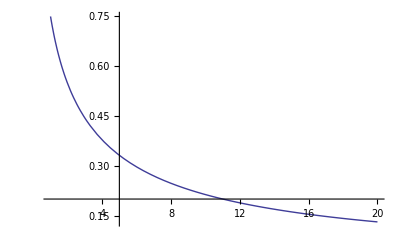

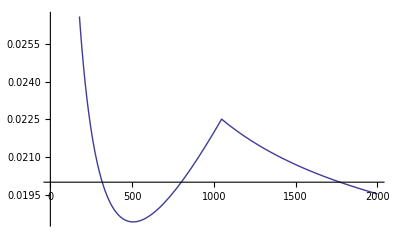

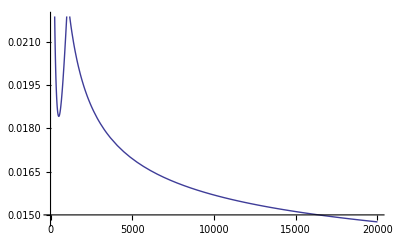

```mathematica
Plot[taugtot[epmax,epmin,epmax,1],{epmax,1,20}]
Plot[taugtot[epmax,epmin,epmax,1],{epmax,1,2000}]
Plot[taugtot[epmax,epmin,epmax,1],{epmax,1,20000}]
```

```mathematica
funD[3]
funDslow[3]
```

-1.33166

-1.33166

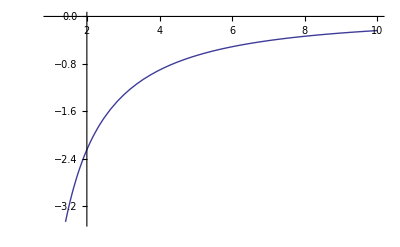

```mathematica
Plot[funD[epmax],{epmax,1,10}]
```

```mathematica
myminsols=FindRoot[funD[epmax]==0,{epmax,2}]
```

{epmax→159.436}

```mathematica
myminsols[[1,2]]
```

159.436

```mathematica
{epmaxerror,epmaxnum,epthicknum,epmaxobs,epmaxminerror,epmaxminnum,epmaxminobs,epmaxmaxerror,epmaxmaxnum,epmaxmaxobs}
```

{1.24345×10^-14,327.237,1,87874.1,5.34017×10^-14,73.5727,19756.7,3.4639×10^-14,9.97684×10^33,2.67912×10^36}

```mathematica
eminobsMeV=0.1;
(*eminobsMeV=1.0; *)
eminobs=eminobsMeV*ergPmev/(me*c^2); (* most strict lower-limit for highest-energy photon *)
epmin=eminobs/gammavalue;
myepmax=327;taugtot[myepmax,epmin,myepmax,1]
myepmax=73.57;taugtot[myepmax,epmin,myepmax,1]
myepmax=10^(34);taugtot[myepmax,epmin,myepmax,1]
```

0.99963

1.00002

0.999973

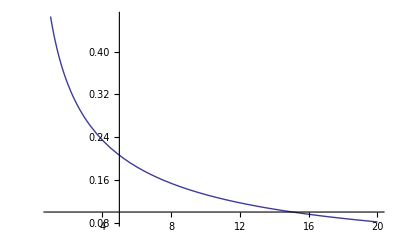

```mathematica
Plot[tauge[ep],{ep,1,20}]
```

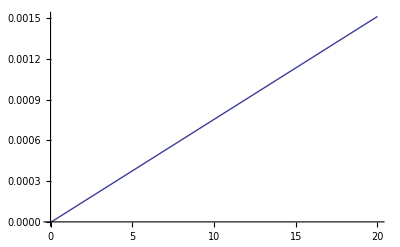

```mathematica
Plot[taugg[ep,epmin,20],{ep,0,20}]
```

```mathematica
epmaxobs/(me*c^2*gammavalue)/ergPmev
```

6.22706×10^39

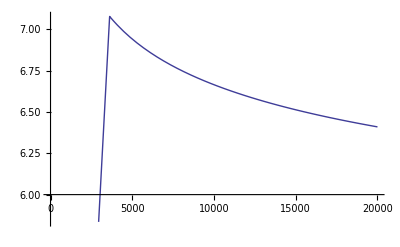

```mathematica
Plot[taugg[epmax,epmin,epmax],{epmax,1,20000}]
```

```mathematica
Plot3D[tauggge[epmax,epmin,epmax,epthick],{epmax,1,20},{epthick,1,10}]
```

-Graphics3D-

```mathematica
(* 12 *)
eminobsMeV=0.1;
(*eminobsMeV=1.0; *)
eminobs=eminobsMeV*ergPmev/(me*c^2); (* most strict lower-limit for highest-energy photon *)
epmin=eminobs/gammavalue;
Plot3D[taugtot[epmax,epmin,epmax,epthick],{epmax,1,20},{epthick,1,10}]
```

-Graphics3D-

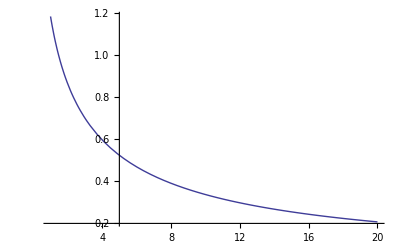

```mathematica
Plot[tauge[ep],{ep,1,20}]
```

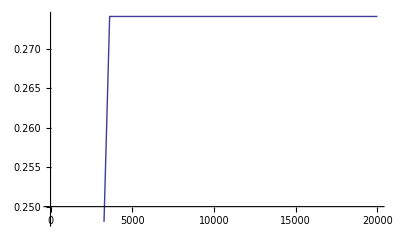

```mathematica
Plot[taugg[ep,epmin,20],{ep,0,20000}]
```

-Graphics3D-

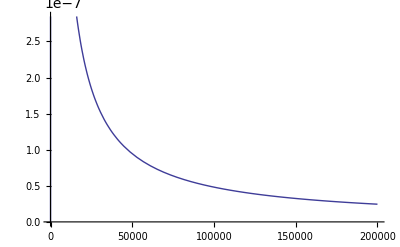

```mathematica
Plot3D[tauggge[epmax,epmin,epmax,epthick],{epmax,1,20000},{epthick,1,10}]
Plot[tauggge[epmax,epmin,epmax,2],{epmax,1,200000}]
```

```mathematica
(* 11 *)
eminobsMeV=0.1;
(*eminobsMeV=1.0; *)
eminobs=eminobsMeV*ergPmev/(me*c^2); (* most strict lower-limit for highest-energy photon *)
epmin=eminobs/gammavalue;
Plot3D[taugtot[epmax,epmin,epmax,epthick],{epmax,1,20},{epthick,1,10}]
Plot3D[taugtot[epmax,epmin,epmax,epthick],{epmax,1,2000},{epthick,1,10}]
```

-Graphics3D-

-Graphics3D-

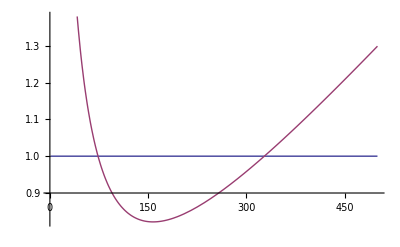

```mathematica
Plot[{1,taugtot[epmax,epmin,epmax,2]},{epmax,1,500}]
```

```mathematica
myepmax=300;
taugtot[myepmax,epmin,myepmax,2]
```

0.958395

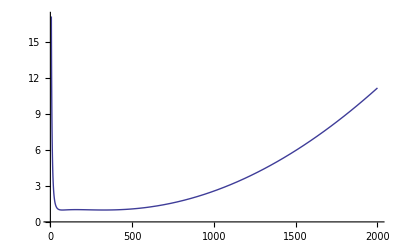

```mathematica
Plot[eqblob[x,2],{x,1,2000}]
```

```mathematica
solsepmax=FindRoot[1==taugtot[x,epmin,x,2],{x,10^3}]
```

{x→327.334}

```mathematica
solsepmax[[1,2]]
```

327.334

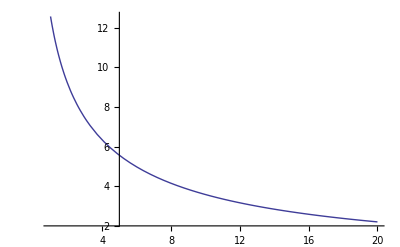

```mathematica
Plot[tauge[ep],{ep,1,20}]
```

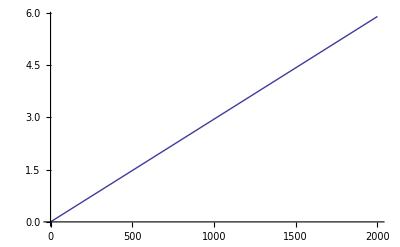

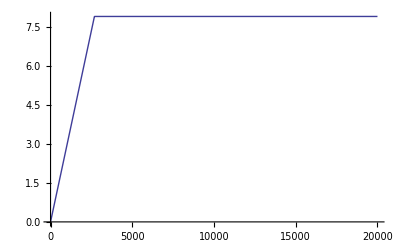

```mathematica
Plot[taugg[ep,epmin,20],{ep,0,2000}]
Plot[taugg[ep,epmin,20],{ep,0,20000}]
```

-Graphics3D-

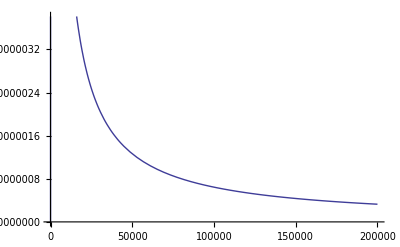

```mathematica
Plot3D[tauggge[epmax,epmin,epmax,epthick],{epmax,1,20000},{epthick,1,10}]
Plot[tauggge[epmax,epmin,epmax,2],{epmax,1,200000}]
```